# Mathematica Project - Predicting Housing Price

## Introduction

Prediction of housing price using different machine learning techniques.-Graphics-

### Synopsis

In this project, we will be using the multiple predictive techniques for predicting the house prices based on the multiple features.
The data contains house sales prices for King County, a popular county in Washington, USA . It include homes sold between May 2014 and May 2015. The dataset mainly contains the  house features, locations( ie latitude and longitude) and price for which the houses were sold. We will be using multiples predictive techniques to find price for the future outcomes.

### Description of variables in the Dataset

The dataset contains 20 house features plus the response variable price with 21613 observations.

id 				: It is the unique numeric number assigned to each house being sold.

date				: It is the date on which the house was sold out.

price			: It is the price of house which we have to predict so this is our target variable and apart from it are our predictor variables.

bedrooms 		: It determines number of bedrooms in a house.

bathrooms 		: It determines number of bathrooms in a bedroom of a house.

sqft_living 		: It is the measurement variable which determines the measurement of house in square foot.

sqft_lot 			: It is also the measurement variable which determines square foot of the lot.

floors			: It determines total floors means levels of house.

waterfront 		: This feature determines whether a house has a view to waterfront 0 means no 1 means yes.

view 			: This feature determines whether a house has been viewed or not 0 means no 1 means yes.

condition		: It determines the overall condition of a house on a scale of 1 to 5.

grade 			: It determines the overall grade given to the housing unit, based on USA grading system on a scale of 1 to 13.

sqft_above		: It determines square footage of house apart from basement.

sqft_basement 	: It determines square footage of the basement of the house.

yr_built 			: It determines the date of building of the house.

yr_renovated 		: It determines year of renovation of house.

zipcode 			: It determines the zipcode of the location of the house.

lat 				: It determines the latitude of the location of the house.

long 			: It determines the longitude of the location of the house.

sqft_living15 		: Living room area in 2015  after the renovations.

sqft_lot15		: lotSize area in 2015 after the renovations.

## Data Pre-Processing

Data preprocessing involves transforming a raw data into an understandable format. In other words data is made readable for the machine learning techniques for the prediction analysis.

#### Importing the data

We all know the structure of the data now and we will import this dataset to work on the regression techniques.

```mathematica
filePath = SystemDialogInput["FileOpen"]; (*Select the CSV file from the file folder for loading the House data*)
HouseData=Import[filePath, "Dataset", HeaderLines-> 1];
HouseData[[1;;10]]
```

Dataset[<>]

The dataset contains 21613 rows and 21 columns.

```mathematica
Dimensions[HouseData]
```

{21613,21}

The variables in the dataset are listed below.

```mathematica
ColumnNames = First@Keys@HouseData
```

Dataset[<>]

#### Data Cleansing and Data Wrangling

Data Cleansing or data cleansing is done for detecting and correcting  corrupt or inaccurate data from a  record, set, table or a dataset. The inaccurate or incomplete data from the dataset is then replaced, modified or deleted according to the analysis.
		Data wrangling  is also referred as data munging. It is the process of transforming  and mapping data from one form to another format with the intent of making it appropriate and valuable for the variety of downstream purposes such as analytics.

Before we start the analysis we need to make sure that there are no missing entries or NAs in the data. If missing values are present either we remove the entire row with the missing entry or change the missing entry with a value suitable with the data. We will also replace the NAs and NANs as well in the dataset.

```mathematica
Count[HouseData, _Missing] (* Check for the missing values in the dataset*)
```

0

As we don’t have any missing values we can proceed with the data for identifying the categorical and numerical variables.The data set has 5 Categorical variables, “floors”, “waterfront”, “view”,  “condition”, “grade”. Since all these are in the form of numbered values we don’t need to convert them as factors for the analysis and we will be able to use them as such going further.

We can split the dataset into Categorical data and numerical data for the convenience in data analysis.

```mathematica
CategoricalVar = ColumnNames[[8;;12]]
```

Dataset[<>]

```mathematica
CategoricalData = Values[Normal[HouseData[[All,8;;12]]]]; (* Categorical variables data*)
```

```mathematica
CategoricalData[[1;;5]]//Dataset
```

Dataset[<>]

```mathematica
NumericalVar = ColumnNames[{3,4,5,6,7,13,14,15,16,17,18,19}] (* Numerical variables in the dataset *)
NumericalVarData = HouseData[[All, {3,4,5,6,7,13,14,15,16,17,18,19}]]; (* Numerical variables data*)
NumericalVarData[[1;;5]]
```

Dataset[<>]

Dataset[<>]

## Data Visualization

Data visualization involves the creation and study of  the visual representation of data. It may be also used to examine the data in graphical format , to obtain additional insights regarding the informations within the data.

### Plots for understanding features of Response variable.

The dataset as contains the details of the houses sold in King County in Washington, USA. We will plot the Map of the city to get familiarise with the city.

```mathematica
GeoGraphics[GeoRange->LinguisticAssistant,GeoRangePadding->LinguisticAssistant,GeoZoomLevel->9,ImageSize->Large]
```

-Graphics-

We can plot the regions where the largest house sales and the lowest house sales happened during the year from May 2014 to 2015 May.

```mathematica
LatLongPriceMax = HouseData[Select[Slot["price"]>1750000&],{3,18,19}] ; (* House location that are having house price more than 2 million dollars*)
LatLongPriceMin = HouseData[Select[Slot["price"]<150000&],{3,18,19}];(*House location that are having house price less than 1.5 billion dollars*)
```

Plotting the Houses location whose price are more than 2 million dollars.

```mathematica
GeoGraphics[{Red,PointSize[0.01],Point[GeoPosition[Values[LatLongPriceMax[SortBy[-#1 &]][[All, 2;;3]]//Normal]]]}, PlotLabel->Style["Street view of House plots whose price are more than 2 million dollars.",16,Bold, Blue], ImageSize->Large]
```

-Graphics-

Plotting the Houses location whose price are less than 1.5 billion dollars.

```mathematica
GeoGraphics[{Black,PointSize[0.01],Point[GeoPosition[Values[LatLongPriceMin[SortBy[-#1 &]][[All, 2;;3]]//Normal]]]}, PlotLabel->Style["Street view of House plots whose price are less than 1.5 billion dollars.",16,Bold, Brown], ImageSize->Large]
```

-Graphics-

## Exploratory Data Analysis

Exploratory data analysis is an approach analyzing data sets to summarize their main characteristics, often with visual methods. EDA is for seeing the what the data can tell us beyond the formal modeling or hypothesis testing task.

Inorder to carry out the Exploratory Data Analysis I am using the below plots in Mathematica
	1. Histogram
	2. Box Plots
	3. List Plot

#### Histogram:

A histogram is an accurate representation of the distribution of numerical data. We can plot the histogram of all numerical variables to understand the normal distribution curve. From this we could further understand the skewness of the variable. Below are the histogram plots for the numerical variables.

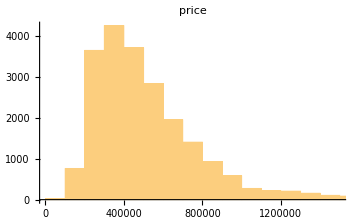
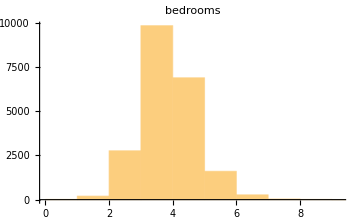
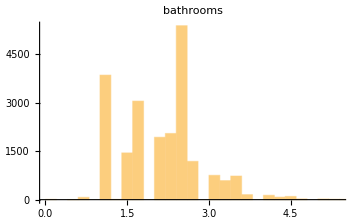
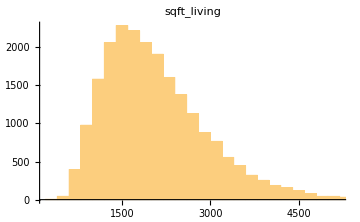
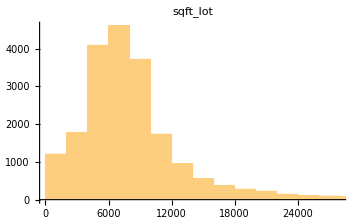
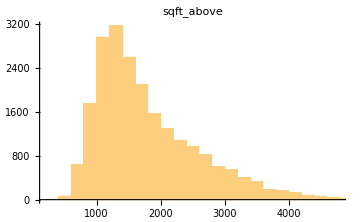
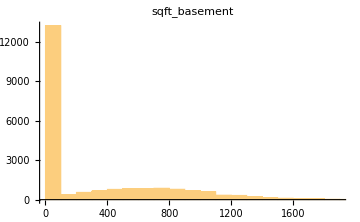
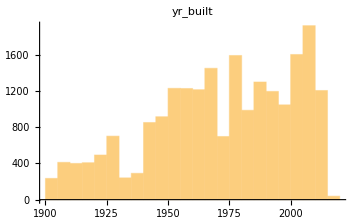

```mathematica
Table[Show[Histogram[NumericalVarData[All, i]//Normal,PlotLabel-> NumericalVar[[i]]],ImageSize -> Medium],{i,1, Dimensions[NumericalVarData][[2]],1}]
```

From the above histogram plots we can see that few variables give the normal distribution and can be standardize. Other variables we need to find the correlation with the target variable for knowing the relevance of it in the models.

#### Box Plot:

A box plot is a method for graphically depicting groups of numerical data through their quantiles. Box plots may also have lines extending vertically from the boxes(whiskers) indicating variability outside the upper and lower quantiles. Outliers can be plotted as the individual point  in the box plots.
We can plot the box plot for the numerical variables and see it there are any outliers in the dataset.

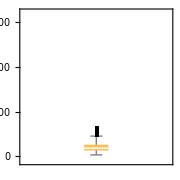
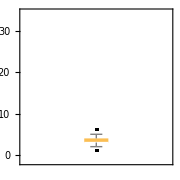
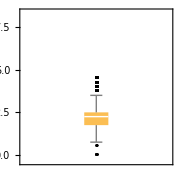
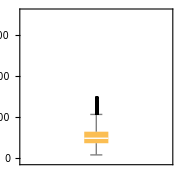
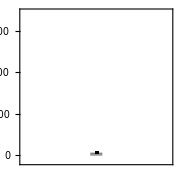
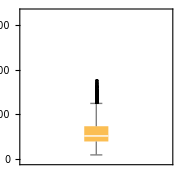
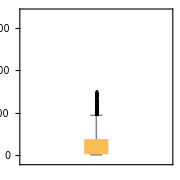
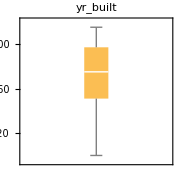

```mathematica
Table[Show[BoxWhiskerChart[NumericalVarData[All, i]//Normal,"Outliers", PlotLabel-> NumericalVar[[i]]],AspectRatio->1, ImageSize -> Small],{i,1, Length[NumericalVar],1}]
```

We are having outliers in the Response variable. If the outliers are significant during the model building we will remove them for performance inprovement,

#### List Plots:

List plot, plots a list of points with specified x and y coordinates. Data can be given in a list format for x and y coordinates. We are plotting the list plot for knowing the relationship between the target variable and predictor variable. Below are the list plots of numerical variable in the dataset.

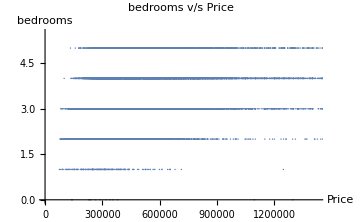
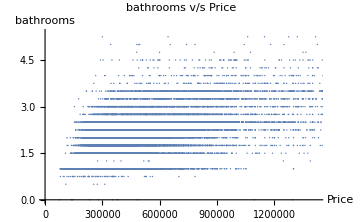
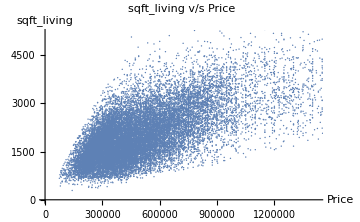
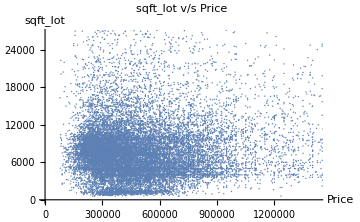
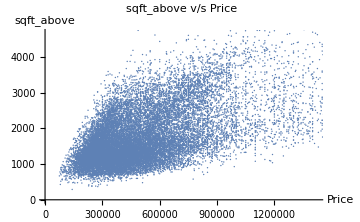
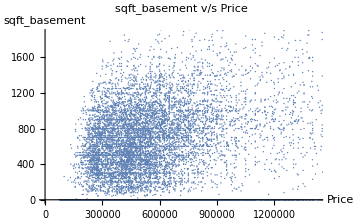
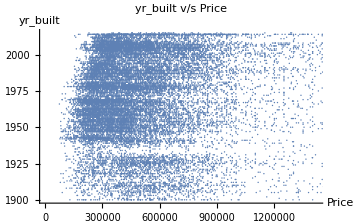
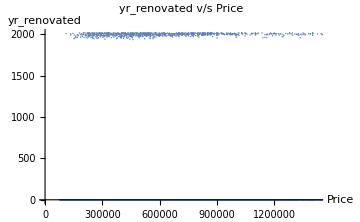

```mathematica
Table[Show[ListPlot[Transpose[{NumericalVarData[[All,1]]//Normal, NumericalVarData[[All,i]]//Normal}],
AxesLabel->{"Price", NumericalVar[[i]]},PlotLabel->Style[ StringForm["`` v/s Price", NumericalVar[[i]]], Red,Bold], ImageSize->Medium]],{i, 2, Dimensions[NumericalVarData][[2]],1}]
```

## Feature Selection

In machine learning and statistics feature selection is also known as variable selection, attribute selection or variable subset selection. It is a process of selecting a subset of relevant features(variables/Predictors) for use in model creation. Feature selection techniques are used for four reasons.
		1. Simplification of models to make them easier to interpret by researchers/users.
		2. Shorter training times.
		3. To avoid the curse of dimensionality.
		4. Enhanced generalization by reducing over-fitting. (formally, reduction of variance)
			The central premise when using the feature selection is that the data contains certain features that are irrelevant or redundant, and can thus be removed from the model without incurring much loss of information.

#### Correlation:

Correlation is a measure of relationship between 2 mathematical variables or measured data values. In other terms correlations is a statistical analysis which shows whether and how strongly a pair of variables are related.

In our dataset the variables “sqft_living15”,”sqft_lot15” and “sqft_living”,”sqft_lot” are highly correlated to each other because the last 2 column variables(ie; “sqft_living15”,”sqft_lot15”)  gives the information of the renovated houses alone. That is whether there is and increase or decrease in the square foot of the living  and square of lot for the renovated houses. So we can remove “sqft_living15”,”sqft_lot15” from the model.

Below codes shows the correlation among these 2 variables and we can see that it is highly correlated with correlation coefficient of more than 70%.

```mathematica
N[Correlation[HouseData[[1;;,6]]//Normal,HouseData[[1;;,20]]//Normal]] (*Finding the correlation between sqft_living and sqft_living15 variable*)
```

0.75642

```mathematica
N[Correlation[HouseData[[1;;,7]]//Normal,HouseData[[1;;,21]]//Normal]](*Finding the correlation between sqft_lot and sqft_lot15 variable*)
```

0.718557

Checking the relevance of Id column with the response variable, price.

```mathematica
IndependenceTest[HouseData[[2;;,3]]//Normal,HouseData[[2;;,1]]//Normal,{"TestDataTable"}]
```

{ | Statistic | P-Value
Spearman Rank | 0.00423094 | 0.53397}

This hypothesis shows that the Id has no relation with the price column. Id & date can be removed from the model since they doesn’t give any relevant information towards the response variable.

Correlations between numerical variable with the Response variable:
 For our data we can find the correlation between the target variable “price” and the predictor variables. From this we will get he rough idea of getting the final predictor variables for the model to perform the deep learning analysis.

```mathematica
Grid[{NumericalVar//Normal,Table[Correlation[NumericalVarData[[All,i]]//Normal, NumericalVarData[[All,1]]//Normal],{i,1,Length[NumericalVar]}]}, Frame->All]
```

price | bedrooms | bathrooms | sqft_living | sqft_lot | sqft_above | sqft_basement | yr_built | yr_renovated | zipcode | lat | long
1. | 0.30835 | 0.525138 | 0.702035 | 0.0896609 | 0.605567 | 0.323816 | 0.0540115 | 0.126434 | -0.0532029 | 0.307003 | 0.0216262

From the above correlation table with the target variable it is clearly visible that the variable “zipcode” has least correlation coefficient and weakly correlated with the target variable, price. We can remove this variable from the model. We can also check the multicollinearity between the numerical variables.

Correlation Matrix Plot:  It is a plot showing correlation coefficient s between sets of variables. Each variable in the Xi in the table is correlated with each of the other values in the table Xj. This allow us to see the pairs with highest correlations.

We can plot a correlation matrix plot with the correlation coefficient and from that we can find the multiple linearity and importance of the predictor variables in the model creation.

```mathematica
corr= Correlation[Values[Normal[NumericalVarData]]]
```

{{1.,0.30835,0.525138,0.702035,0.0896609,0.605567,0.323816,0.0540115,0.126434,-0.0532029,0.307003,0.0216262},{0.30835,1.,0.515884,0.576671,0.0317032,0.4776,0.303093,0.154178,0.0188408,-0.152668,-0.00893101,0.129473},{0.525138,0.515884,1.,0.754665,0.0877397,0.685342,0.28377,0.506019,0.050739,-0.203866,0.024573,0.223042},{0.702035,0.576671,0.754665,1.,0.172826,0.876597,0.435043,0.318049,0.0553629,-0.19943,0.0525295,0.240223},{0.0896609,0.0317032,0.0877397,0.172826,1.,0.183512,0.0152862,0.0530804,0.00764351,-0.129574,-0.0856828,0.229521},{0.605567,0.4776,0.685342,0.876597,0.183512,1.,-0.0519433,0.423898,0.0232847,-0.26119,-0.000816499,0.343803},{0.323816,0.303093,0.28377,0.435043,0.0152862,-0.0519433,1.,-0.133124,0.0713229,0.0748446,0.110538,-0.144765},{0.0540115,0.154178,0.506019,0.318049,0.0530804,0.423898,-0.133124,1.,-0.224874,-0.346869,-0.148122,0.409356},{0.126434,0.0188408,0.050739,0.0553629,0.00764351,0.0232847,0.0713229,-0.224874,1.,0.0643571,0.0293976,-0.0683724},{-0.0532029,-0.152668,-0.203866,-0.19943,-0.129574,-0.26119,0.0748446,-0.346869,0.0643571,1.,0.267048,-0.564072},{0.307003,-0.00893101,0.024573,0.0525295,-0.0856828,-0.000816499,0.110538,-0.148122,0.0293976,0.267048,1.,-0.135512},{0.0216262,0.129473,0.223042,0.240223,0.229521,0.343803,-0.144765,0.409356,-0.0683724,-0.564072,-0.135512,1.}}

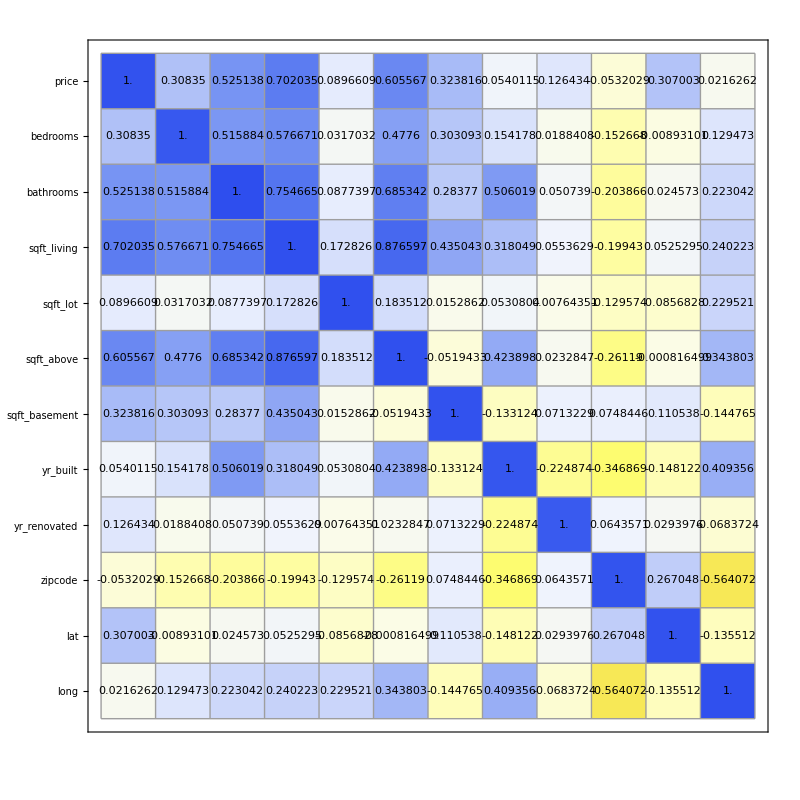

```mathematica
heading={{Table[{i,NumericalVar[[i]]},{i,1,Length@NumericalVar}],None},{None,Table[{i,Rotate[NumericalVar[[i]],90 Degree]},{i,1,Length@NumericalVar}]}};
Show[MatrixPlot[corr,Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[corr],{2}]},Mesh->True,ColorFunction->ColorData[{"TemperatureMap","Reverse"}],FrameTicks->heading], ImageSize->{800,800}]
```

From the above correlation table we could come into a conclusion that the predictor variable zipcode is not a relevant variable for the model creation and hence we can exclude this variable in creation of the model.

## Feature Scaling

Feature scaling is a method to standardize the range of independent variable or the features of data.

From histogram we can arrive at an inference that few variables are having normal distribution and we can standardize them before creating the model. Also we can remove the variable zipcode from the predictor variables.

```mathematica
Dimensions[NumericalVarData]
```

{21613,12}

```mathematica
StdNumericalData = Values[Normal[NumericalVarData[[All,{1,2,3,4,5,6,7,8,9,11,12}]]]];
StdNumericalData[[1;;,1]]=N[Standardize[StdNumericalData [[1;;,1]]]];
StdNumericalData[[1;;,2]]=N[Standardize[StdNumericalData [[1;;,2]]]];
StdNumericalData[[1;;,4]]=N[Standardize[StdNumericalData [[1;;,4]]]];
StdNumericalData[[1;;,5]]=N[Standardize[StdNumericalData [[1;;,5]]]];
StdNumericalData[[1;;,6]]=N[Standardize[StdNumericalData [[1;;,6]]]];
```

```mathematica
StdNumericalData[[1;;10]]
```

{{-0.866697,-0.398728,1,-0.979812,-0.228316,-0.734691,0,1955,0,47.5112,-122.257},{-0.00568779,-0.398728,2.25,0.533622,-0.189881,0.46083,400,1951,1991,47.721,-122.319},{-0.980827,-1.47393,1,-1.42622,-0.123296,-1.22981,0,1933,0,47.7379,-122.233},{0.174086,0.676469,3,-0.130547,-0.244009,-0.891678,910,1965,0,47.5208,-122.393},{-0.0819556,-0.398728,2,-0.435412,-0.169649,-0.130892,0,1987,0,47.6168,-122.045},{1.8656,0.676469,4.5,3.63671,2.09614,2.5379,1530,2001,0,47.6561,-122.005},{-0.769728,-0.398728,2.25,-0.397303,-0.200093,-0.0886264,0,1995,0,47.3097,-122.327},{-0.676164,-0.398728,1.5,-1.11047,-0.130273,-0.879602,0,1963,0,47.4095,-122.315},{-0.845996,-0.398728,1,-0.326531,-0.184376,-0.891678,730,1960,0,47.5123,-122.337},{-0.591316,-0.398728,2.5,-0.206763,-0.206346,0.122703,0,2003,0,47.3684,-122.031}}

```mathematica
Dimensions[StdNumericalData]
```

{21613,11}

```mathematica
newHouseData = Table[Join[StdNumericalData[[i, All]], CategoricalData[[i,All]]],{i,1,Length[StdNumericalData]}]
```

{{-0.866697,-0.398728,1,-0.979812,-0.228316,-0.734691,0,1955,0,47.5112,-122.257,1,0,0,3,7},{-0.00568779,-0.398728,2.25,0.533622,-0.189881,0.46083,400,1951,1991,47.721,-122.319,2,0,0,3,7},21609,{-0.381579,-0.398728,2.5,-0.522516,-0.307069,-0.2275,0,2004,0,47.5345,-122.069,2,0,0,3,8},{-0.585868,-1.47393,0.75,-1.15402,-0.338744,-0.927906,0,2008,0,47.5941,-122.299,2,0,0,3,7}}
 |  |  |  |

## Modelling

Model selection is a task of selecting the statistical model from a set of candidate models from a given dataset. The model can also be a mathematical equation that describes the relationships among the predictor variables and response variables in a dataset.  The model is divided into train and test data. Train data set is used to train the model for predicting the desired output by using different machine learning techniques. Test data is used for validating the predicted model for the prediction of response variable and finally comparing the error with the previous value of response variable before prediction analysis.

### Training and test Dataset:

```mathematica
TrainData = newHouseData[[1;;Round[Length[newHouseData]*.8],All]];
TestData = newHouseData[[Round[Length[newHouseData]*.8]+1;;,All]];
```

```mathematica
Dimensions[TrainData]
Dimensions[TestData]
```

{17290,16}

{4323,16}

```mathematica
TrainDataNew = TrainData[[All,2;;]]
```

{{-0.398728,1,-0.979812,-0.228316,-0.734691,0,1955,0,47.5112,-122.257,1,0,0,3,7},{-0.398728,2.25,0.533622,-0.189881,0.46083,400,1951,1991,47.721,-122.319,2,0,0,3,7},17286,{-0.398728,4.25,3.34273,-0.176409,2.87602,980,1954,0,47.6288,-122.282,2.5,0,2,3,11},{0.676469,4.5,1.4591,-0.185101,1.97033,0,2014,0,47.6875,-122.33,3,0,0,3,9}}
 |  |  |  |

```mathematica
TestDatanew= TestData[[All, 2;;]]
```

{{0.676469,2.5,0.206981,-0.0870817,-0.299956,730,1967,0,47.7089,-122.241,1,0,0,3,8},{0.676469,2.5,0.206981,-0.0870817,-0.299956,730,1967,0,47.7089,-122.241,1,0,0,3,8},4319,{-0.398728,2.5,-0.522516,-0.307069,-0.2275,0,2004,0,47.5345,-122.069,2,0,0,3,8},{-1.47393,0.75,-1.15402,-0.338744,-0.927906,0,2008,0,47.5941,-122.299,2,0,0,3,7}}
 |  |  |  |

```mathematica
model=Table[TrainDataNew[[i,All]]-> TrainData[[i,1]],{i,1,Length[TrainData],1}];
```

```mathematica
model[[1;;5]]
```

{{-0.398728,1,-0.979812,-0.228316,-0.734691,0,1955,0,47.5112,-122.257,1,0,0,3,7}→-0.866697,{-0.398728,2.25,0.533622,-0.189881,0.46083,400,1951,1991,47.721,-122.319,2,0,0,3,7}→-0.00568779,{-1.47393,1,-1.42622,-0.123296,-1.22981,0,1933,0,47.7379,-122.233,1,0,0,3,6}→-0.980827,{0.676469,3,-0.130547,-0.244009,-0.891678,910,1965,0,47.5208,-122.393,1,0,0,5,7}→0.174086,{-0.398728,2,-0.435412,-0.169649,-0.130892,0,1987,0,47.6168,-122.045,1,0,0,3,8}→-0.0819556}

```mathematica
TestDataFinal = Table[TestDatanew[[i,All]]-> TestData[[i,1]],{i,1,Length[TestData],1}];
```

```mathematica
TestDataFinal[[1;;5]]
```

{{0.676469,2.5,0.206981,-0.0870817,-0.299956,730,1967,0,47.7089,-122.241,1,0,0,3,8}→-0.436056,{0.676469,2.5,0.206981,-0.0870817,-0.299956,730,1967,0,47.7089,-122.241,1,0,0,3,8}→0.231015,{-0.398728,2.5,-0.66406,-0.321772,-0.758843,310,2005,0,47.5472,-121.998,2,0,0,3,8}→-0.436683,{-0.398728,1.75,-0.870932,0.0263887,-0.91583,250,1976,0,47.7427,-122.071,1,0,0,3,8}→-0.54501,{0.676469,2.75,0.81671,-0.168539,1.25784,0,2005,0,47.4863,-122.14,2,0,0,3,8}→-0.0669744}

### Linear Regression:

Linear regression is a linear approach to modelling the relationship between a scalar response (or dependent variable) and one or more explanatory variables (or independent variables). The case of one explanatory variable is called simple linear regression. For more than one explanatory variable, the process is called multiple linear regression.

#### Train Models

Normalisation and standardisation of  Numerical data is done by using mathematical functions for the train dataset.

```mathematica
predictorAlgLR=Predict[model,Method->"LinearRegression"]
```

PredictorFunction[…]

#### Validate Test Models

```mathematica
PredictmeaLR = PredictorMeasurements[predictorAlgLR, TestDataFinal]
```

PredictorMeasurementsObject[…]

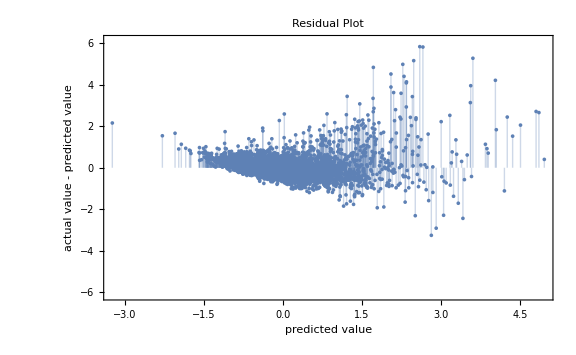

```mathematica
Show[PredictmeaLR[ "ResidualPlot"],PlotLabel-> Style["Residual Plot", 16,Blue,Bold],ImageSize->Large]
```

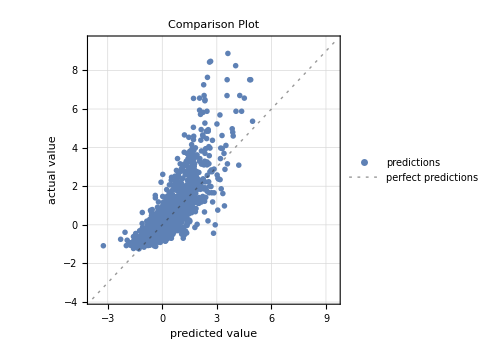

```mathematica
Show[PredictmeaLR ["ComparisonPlot"],PlotLabel-> Style["Comparison Plot", 16,Blue,Bold],ImageSize->Medium]
```

Finding Accuracy of the model

```mathematica
PredictedPrice = predictorAlgLR[TestDatanew];
ActualPrice = TestData[[All,1]];
SSE = Total[(ActualPrice - PredictedPrice)^2];
SSR = Total[(PredictedPrice - Mean[ActualPrice])^2];
Rsquare = SSR /(SSR + SSE)
```

0.671501

Mean squared error

```mathematica
MSE = SSE/(Length[TestDatanew]-15)
```

0.334328

The mean square error of the variable is  0.334 and the accuracy of the model is around 67%. Least the mean square error value higher the accuracy.

```mathematica
PredictorInformation[predictorAlgLR]
```

Predictor information
Input type | Mixed (number: 15)
Method | LinearRegression
Standard deviation | 0.461 ± 0.017
Loss | 0.649 ± 0.022
Single evaluation time | 7.13 ms/example
Batch evaluation speed | 22.4 examples/ms
Predictor memory | 334. kB
Training examples used | 17290 examples
Training time | 16.6 s
 |

### Random Forest:

Random forests or random decision forests are an ensemble learning method for classification, regression and other tasks, that operated by constructing decision trees at training time and outputting the class that is the mode of the classes (classification) or mean prediction (regression) of the individual trees.

#### Train Model

```mathematica
predictorAlgRandomF=Predict[model,Method->"RandomForest"]
```

PredictorFunction[…]

#### Validate Test Models

```mathematica
PredictmeaRandomF= PredictorMeasurements[predictorAlgRandomF, TestDataFinal]
```

PredictorMeasurementsObject[…]

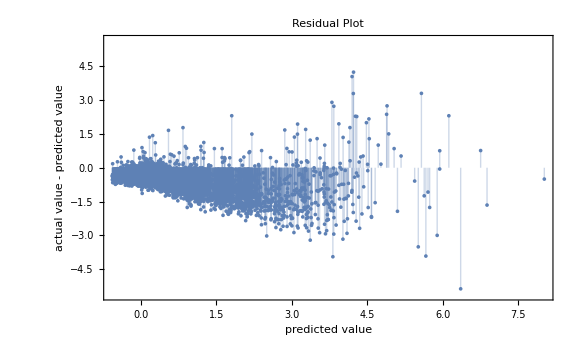

```mathematica
Show[PredictmeaRandomF /@ {"ResidualPlot"},PlotLabel-> Style["Residual Plot", 16,Blue,Bold], ImageSize-> Large]
```

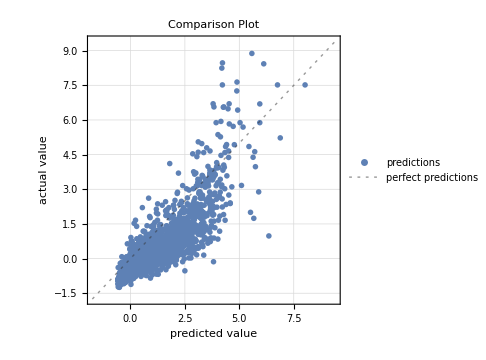

```mathematica
Show[PredictmeaRandomF /@ {"ComparisonPlot"},PlotLabel-> Style["Comparison Plot", 16,Blue,Bold], ImageSize-> Medium]
```

Finding Accuracy of the model

```mathematica
PredictedPrice = predictorAlgRandomF[TestDatanew];
ActualPrice = TestData[[All,1]];
SSE = Total[(ActualPrice - PredictedPrice)^2];
SSR = Total[(PredictedPrice - Mean[ActualPrice])^2];
Rsquare= SSR /(SSR + SSE)
```

0.69028

Mean squared error

```mathematica
MSE = SSE/(Length[TestDatanew]-15)
```

0.73752

Even though the R square value for the model is lesser the mean squared error is more compared to the other models. So its accuracy is the least of all 4 models.

```mathematica
PredictorInformation[predictorAlgRandomF]
```

Predictor information
Input type | Mixed (number: 15)
Method | RandomForest
Standard deviation | 0.565 ± 0.055
Loss | 0.856 ± 0.11
Single evaluation time | 12.7 ms/example
Batch evaluation speed | 6.53 examples/ms
Predictor memory | 803. kB
Training examples used | 17290 examples
Training time | 9.71 s
 |

### Nearest Neighbour:

Nearest neighbour analysis examines the distances between each point(variable) and the closest point to it, and then compares these to expected values for a random sample of points from a CSR (complete spatial randomness) pattern.

#### Train Model

```mathematica
predictorAlgNN=Predict[model,Method->"NearestNeighbors"]
```

PredictorFunction[…]

#### Validate Test Model

```mathematica
PredictmeaNN= PredictorMeasurements[predictorAlgNN, TestDataFinal]
```

PredictorMeasurementsObject[…]

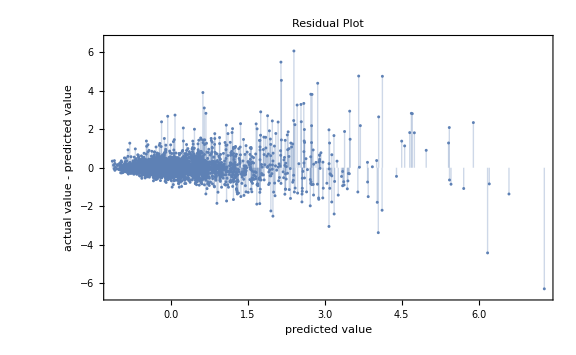

```mathematica
Show[PredictmeaNN/@ {"ResidualPlot"},PlotLabel-> Style["Residual Plot", 16,Blue,Bold], ImageSize-> Large]
```

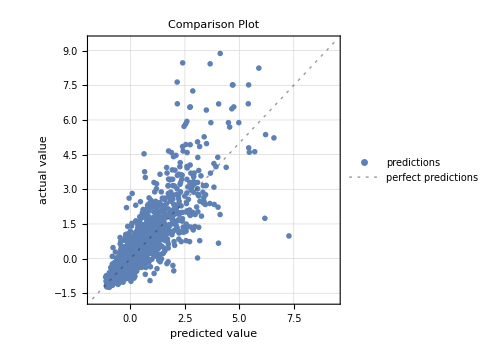

```mathematica
Show[PredictmeaNN/@ {"ComparisonPlot"},PlotLabel-> Style["Comparison Plot", 16,Blue,Bold], ImageSize-> Medium]
```

Finding Accuracy of the model

```mathematica
PredictedPrice = predictorAlgNN[TestDatanew];
ActualPrice = TestData[[All,1]];
SSE = Total[(ActualPrice - PredictedPrice)^2];
SSR = Total[(PredictedPrice - Mean[ActualPrice])^2];
Rsquare = SSR /(SSR + SSE)
```

0.743534

Mean squared error

```mathematica
MSE = SSE/(Length[TestDatanew]-15)
```

0.253062

The nearest neighbour shows a good mean squared value around 0.25 and has an accuracy giving around 75%. This is the second best model among all 4 models.

```mathematica
PredictorInformation[predictorAlgNN]
```

Predictor information
Input type | Mixed (number: 15)
Method | NearestNeighbors
Standard deviation | 0.437 ± 0.03
Loss | 0.0904 ± 0.034
Single evaluation time | 6.67 ms/example
Batch evaluation speed | 2.17 examples/ms
Predictor memory | 1.91 MB
Training examples used | 17290 examples
Training time | 19.1 s
 |

### Gradient Boosted Trees:

Gradient Boosted Trees is a machine learning technique for regression and classification problems, which produces a prediction model in the form of an ensemble of weak prediction models, typically decision trees. It builds the model in a stage like fashion and it generalizes them by  allowing optimization of an arbitrary differentiable loss function.

#### Train Model

```mathematica
predictorAlgGBT=Predict[model,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

#### Validate Test Model

```mathematica
PredictmeaGBT= PredictorMeasurements[predictorAlgGBT, TestDataFinal]
```

PredictorMeasurementsObject[…]

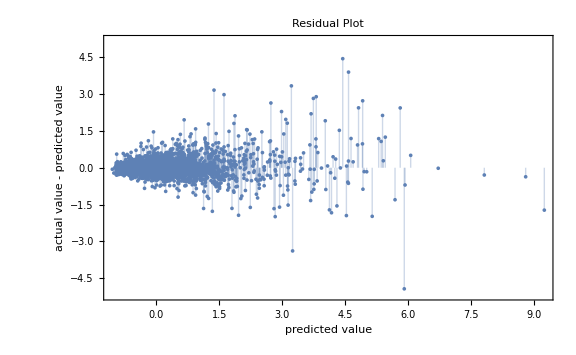

```mathematica
Show[PredictmeaGBT/@ {"ResidualPlot"},PlotLabel-> Style["Residual Plot", 16,Blue,Bold],ImageSize-> Large]
```

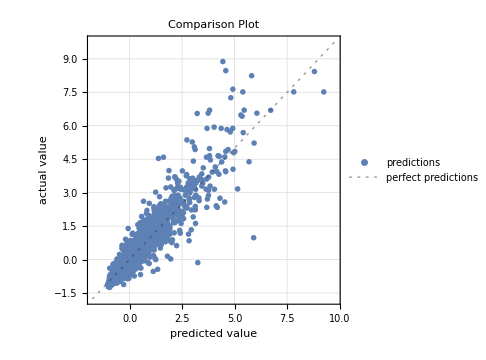

```mathematica
Show[PredictmeaGBT/@ {"ComparisonPlot"},PlotLabel-> Style["Comparison Plot", 16,Blue,Bold],ImageSize-> Medium]
```

Finding Accuracy of the model

```mathematica
PredictedPrice = predictorAlgGBT[TestDatanew];
ActualPrice = TestData[[All,1]];
SSE = Total[(ActualPrice - PredictedPrice)^2];
SSR = Total[(PredictedPrice - Mean[ActualPrice])^2];
Rsquare = SSR /(SSR + SSE)
```

0.871145

Mean Squared Error

```mathematica
MSE = SSE/(Length[TestDatanew]-15)
```

0.125852

This being the best model shows an accuracy of 88% and a mean squared error of 0.126. This is the best model out of all 4 models.

```mathematica
PredictorInformation[predictorAlgGBT]
```

Predictor information
Input type | Mixed (number: 15)
Method | GradientBoostedTrees
Standard deviation | 0.325 ± 0.012
Loss | 0.103 ± 0.033
Single evaluation time | 12.4 ms/example
Batch evaluation speed | 7.57 examples/ms
Predictor memory | 527. kB
Training examples used | 17290 examples
Training time | 28.8 s
 |

## Conclusion

Since our target variable was price we had outliers which were crucial in the model building and hence I haven’t removed the outliers from the data. The best model was created by Gradient Boosted Tree technique and it has the least mean square error and has an accuracy of 88%. All the other models accuracy where lesser than the Gradient boosted tree technique.Out of 4 models the least significant model was Random forest technique.